#### Eigenvalues of CPSWFs Hamed Baghal Ghaffari hamed.baghalghaffari@newcastle.edu.au Date: 2025-Feb-06 If you use this code you can cite my thesis @phdthesis{ghaffari2022higher, title={Higher-dimensional Prolate Spheroidal Wave Functions}, author={Baghal Ghaffari, Hamed}, year={2022}, school={The University of Newcastle} }

```mathematica
Evenprolate[k_,c_,m_]:=(
M=ConstantArray[0,{m,m}];
M[[1,1]]=(4* Pi^2) *(c^2) (k+1)/(k+2); 
For[i=1,i≤m-1,i++,
M[[i,i+1]]=-(4 *Pi^2)* (c^2)* ((i) *(k+i))/((k+2 i)* Sqrt[(k+2 i+1)* (k+2 i-1)]);
];
For[i=2,i≤m,i++,
M[[i,i]]=4 *(i-1) *(k+i)+4 *Pi^2 *c^2 *(((i+k)^2)/((2 i+k)* (2 i+k-1))+((i-1)^2)/((2 i+k-2)* (2 i+k-1)));
];
For[i=1,i≤m-1,i++,
M[[i+1,i]]=-(4 *Pi^2)* (c^2)* ((i) *(k+i))/((k+2 i)* Sqrt[(k+2 i+1)* (k+2 i-1)]);
];
Return[N[M]]
)
```

```mathematica
Evencoefficientprolate[k_,c_,m_,n_]:=(
M=Evenprolate[k,c,m];
{eigs,vecs}=N[Eigensystem[M]];
     list1=Partition[Riffle[eigs,vecs],2];
     list2=Sort[list1,#1[[1]]<#2[[1]]&];
Return[list2[[n,2]]]
)
```

```mathematica
Evencliffordlegendreradialpart[r_,N_,k_]:=Module[{C,i,D},If[N==0,C=1,C=((2^(2 *N)*Gamma[2 N+1])/Gamma[N+1]) *((Gamma[k+N+1]/Gamma[k+1]));
For[i=1,i<=N,i++,C=C+((2^(2*N)*Gamma[2*N+1])/Gamma[N+1])*(Binomial[N,i] *(Gamma[i+k+N+1]/Gamma[i+k+1])*(-1)^i )*r^(2*i);];];
D=(Sqrt[(2 k)+(4 *N)+2]/(2^(2 *N) Factorial[2 *N])) C;
D]
```

```mathematica
N[Evencliffordlegendreradialpart[0.67,3,2]]
```

-3.56803

```mathematica
Evencomputemultiprolateradialpart[r_,k_,c_,m_,n_]:=Module[{G,N},G=0;
N=Evencoefficientprolate[k,c,m+n,n];
Do[If[Abs[N[[j]]]>1/1000000,G=G+N[[j]]*Evencliffordlegendreradialpart[r,j-1,k]],{j,Length[N]}];
G]
```

```mathematica
Evencomputemultiprolateradialpart[0.4,1,3,20,1]
```

6.03423

```mathematica
EvenquatientFourieronprolateatzero[k_,c_,m_,n_]:=Module[{N,q},N=Evencoefficientprolate[k,c,m,n];
q=-N[[1]]*Sqrt[2 k+2]*Pi^(k+1)*c^k*(I^k)/(Gamma[k+2]*Evencomputemultiprolateradialpart[0,k,c,m,n]);
q]
```

```mathematica
EvenquatientFourieronprolateatzero[4,1,20,1]
```

-0.624522

```mathematica
Oddprolate[k_,c_,m_]:=(
M=ConstantArray[0,{m,m}];
For[i=1,i≤m-1,i++,
M[[i,i+1]]=-(4*(Pi)^2)*(c^2)*((i)*(k+i+1))/((k+2*i+1)*Sqrt[(k+2*i+2)*(k+2*i)]);
];
For[i=1,i≤m,i++,
M[[i,i]]=4*(i)*(k+i)+4*((Pi)^2)*(c^2)*((((i+k)^2)/((2*i+k-1)*(2*i+k)))+(((i)^2)/((2*i+k+1)*(2*i+k))));
];
For[i=1,i≤m-1,i++,
M[[i+1,i]]=-(4*(Pi)^2)*(c^2)*((i)*(k+i+1))/((k+2*i+1)*Sqrt[(k+2*i+2)*(k+2*i)]);
];
Return[N[M]]
)
```

```mathematica
Oddcoefficientprolate[k_,c_,m_,n_]:=(
M=Oddprolate[k,c,m];
{eigs,vecs}=N[Eigensystem[M]];
     list1=Partition[Riffle[eigs,vecs],2];
     list2=Sort[list1,#1[[1]]<#2[[1]]&];
Return[list2[[n,2]]]
)
```

```mathematica
Oddcliffordlegendreradialpart[r_,N_,k_]:=Module[{C,i,D},If[N==0,C=-2,C=-((2^(2*N+1)*Gamma[2*N+2])/Gamma[N+1])*((Gamma[k+N+2]/Gamma[k+2]));
For[i=1,i<=N,i++,C=C-((2^(2*N+1)*Gamma[2*N+2])/Gamma[N+1])*(Binomial[N,i] (Gamma[i+k+N+2]/Gamma[i+k+2])*(-1)^i*(r^(2*i)));];];
D=(Sqrt[(2*k)+(4*N)+4]/(2^(2*N+1)*Factorial[2*N+1])) C;
D]
```

```mathematica
Oddcliffordlegendreradialpart[0.24,2,3]
```

-53.7699

```mathematica
Oddcomputemultiprolateradialpart[r_,k_,c_,m_,n_]:=Module[{G,N},G=0;
N=Oddcoefficientprolate[k,c,m+n,n];
Do[If[Abs[N[[j]]]>1/1000000,G=G+N[[j]]*Oddcliffordlegendreradialpart[r,j-1,k]],{j,Length[N]}];
G]
```

```mathematica
-Oddcomputemultiprolateradialpart[0.24,1,1,20,1]
```

9.76411

```mathematica
OddquatientFourieronprolateatzero[k_,c_,m_,n_]:=Module[{N,q},N=Oddcoefficientprolate[k,c,m,n];
q=N[[1]]*Sqrt[2 k+4]*Pi^(k+2)*c^(k+1)*(I^(k+1))/(Gamma[k+3]*Oddcomputemultiprolateradialpart[0,k,c,m,n]);
q]
OddquatientFourieronprolateatzero[1,2,20,1]
```

0.500001

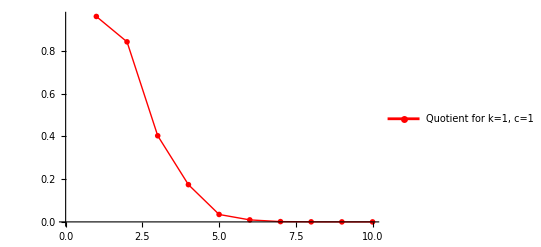

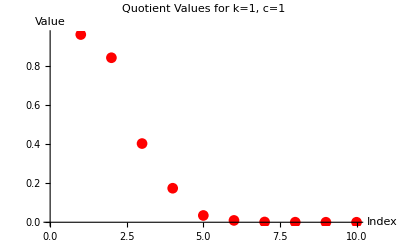

```mathematica
(*Initialize the T array with zeros*)T=ConstantArray[0,10];

(*Compute values for even and odd quotient functions*)
Do[T[[2*n-1]]=Abs[EvenquatientFourieronprolateatzero[2,1,40,n]];
T[[2*n]]=Abs[OddquatientFourieronprolateatzero[2,1,40,n]];,{n,1,5}];

(*Plot the results*)
ListPlot[T,Joined->True,PlotStyle->{Red,Thick},PlotMarkers->{"o",12},PlotLegends->Placed[{"Quotient for k=1, c=1"},Above],PlotMarkers->None]

(*Overlay the second plot with markers*)
Show[ListPlot[T,PlotStyle->{Red},PlotMarkers->Automatic],AxesLabel->{"Index","Value"},LabelStyle->{FontSize->20},PlotLabel->"Quotient Values for k=1, c=1"]
```

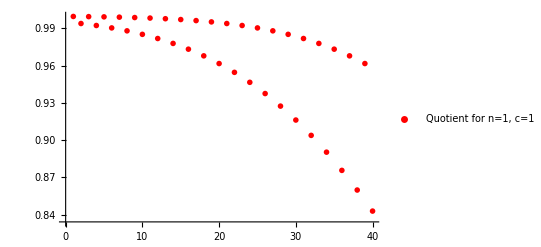

```mathematica
(*Initialize the T array with zeros*)T=ConstantArray[0,40];

(*Compute values for even and odd quotient functions*)
Do[T[[2*k-1]]=Abs[EvenquatientFourieronprolateatzero[k/10,1,40,1]];
T[[2*k]]=Abs[OddquatientFourieronprolateatzero[k/10,1,40,1]];,{k,1,20}];

(*Plot the results*)
ListPlot[T,Joined->False,PlotStyle->{Red,Thick},PlotMarkers->{"o",12},PlotLegends->Placed[{"Quotient for n=1, c=1"},Above],PlotMarkers->None]

(*Overlay the second plot with markers*)
```

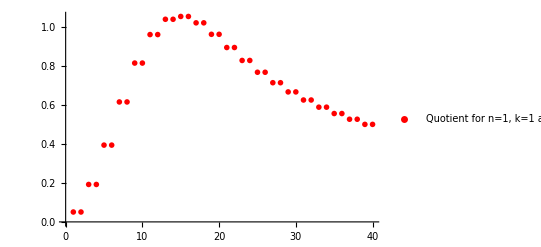

```mathematica
(*Initialize the T array with zeros*)T=ConstantArray[0,40];

(*Compute values for even and odd quotient functions*)
Do[T[[2*c-1]]=Abs[EvenquatientFourieronprolateatzero[2,c/10,40,1]];
T[[2*c]]=Abs[OddquatientFourieronprolateatzero[1,c/10,40,1]];,{c,1,20}];

(*Plot the results*)
ListPlot[T,Joined->False,PlotStyle->{Red,Thick},PlotMarkers->{"o",12},PlotLegends->Placed[{"Quotient for n=1, k=1 and n=0 k=2"},Above],PlotMarkers->None]

(*Overlay the second plot with markers*)
```